{{g→Function[{t},ⅇ^(-2.5 t) (5.92405×10^-15 ⅇ^(1.5 t)-1.15903×10^-14 ⅇ^(2. t)+100. ⅇ^(2.5 t))],m→Function[{t},-200. ⅇ^(-2.5 t) (-7.56246×10^-17 ⅇ^(1.5 t)+1. ⅇ^(2. t)-1. ⅇ^(2.5 t))],p→Function[{t},-800. ⅇ^(-2.5 t) (-0.5 ⅇ^(1.5 t)+1. ⅇ^(2. t)-0.5 ⅇ^(2.5 t))]}}

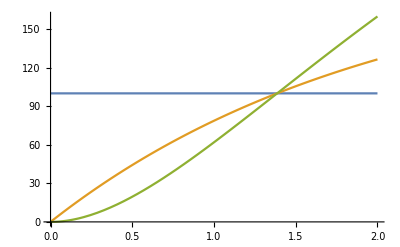

{{126.424},{159.831}}

```mathematica
ClearAll["Global`*"]
(*NOTE: x*x ≠ xsq*)
(*G -> G+M, M -> M + P, M -> 0, P -> 0*)
V = 100;
c={1, 2, 0.5, 1};
eqns={g'[t]==0,
m'[t]==c[[1]]g[t]-c[[3]]m[t],
p'[t]==c[[2]]m[t]-c[[4]]p[t],
g[0]==V,m[0]==0,p[0]==0};
sol=DSolve[eqns,{g,m,p},t]
Plot[{g[t]/.sol,m[t]/.sol,p[t]/.sol},{t,0,2}]
N[{m[t]/.sol,p[t]/.sol}/.{t->2},12]
```